```mathematica
Remove["Global`*"]
```

```mathematica
spike:=Piecewise[{{1,#==0},{0,#≠0}}]&
Convolve[DiracDelta[x],PDF[NormalDistribution[μ,σ],x],x,y]
```

(ⅇ^(-(y-μ)^2/(2 σ^2)))/(√(2 π) σ)

SparseArray[<10>, {1000, 1000}]

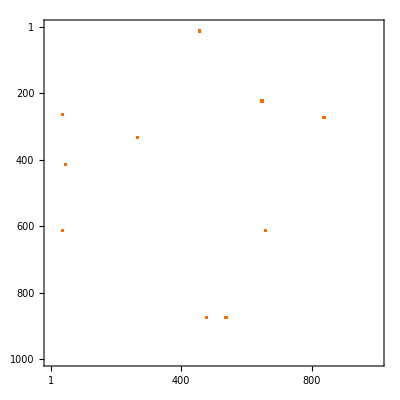

```mathematica
arr=SparseArray[Table[RandomInteger[{1,1000},2]->1,{i,10}],{1000,1000},0]
MatrixPlot[arr]
```

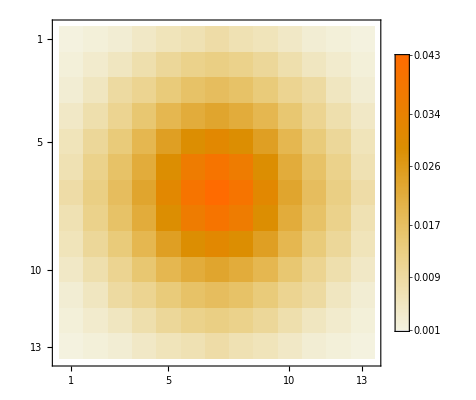

```mathematica
ker=GaussianMatrix[{6,2}];
MatrixPlot[ker,PlotLegends->Automatic]
```

```mathematica
convarr=ListConvolve[ker,arr,{1,1},0];
MatrixPlot[GaussianFilter[arr,{6,2}],PlotLegends->Automatic]
MatrixPlot[convarr,PlotLegends->Automatic]
```

-Graphics-

-Graphics-

```mathematica
f[x_]=PDF[NormalDistribution[0,3],x]
```

(ⅇ^(-x^2/18))/(3 √(2 π))

```mathematica
f[0]^2//N
```

0.0176839